# Sprott: Bulk Implementation

### Sprott Problem Definitions

These use the top ± definition from Sprott when there is a choice. The only exception here is #4 where there is a typo in the table.The ancillary functions and derivatives are defined.  Jump discontinuities are smoothed using tanh(m x) with a default value of m=50.  All problems have parameters {a,b,c,d,m}.  The smoothing parameter is only active in problems 11, 12, and 13.  The functions fSprott[p][y], dyfSprott[p][y] and dpfSprott[p][y] are defined and protected at the bottom of the initialization cell.

Note:  There is an inconsistency in the choices of ± signs in the 4th IVP in the paper.  The given IC diverge rapidly. I changed the IC to (0,-1,0)

```mathematica
Unprotect[Sprott, fSprott,dyfSprott];
Clear[Sprott, fSprott,Di,Dip,Rd,Rdp,Sa,Sap,Sg,Sgp,He,Hep,Absp,a,b,c,d,m]
Sprott=<|1-><|"fun":>-a ypp+b yp-c y+d yp^2,"par"->{2.017,0,1,1,50},"IC"->{0,0,1},"dery":>{-c,b+2 d yp,-a},"derp":>{-ypp,yp,-y,yp^2},"lam"->{0.055,0,-2.072}|>,2-><|"fun":>a ypp-b yp+c y+d y^2,"par"->{0,2.8,1,1,50},"IC"->{-0.5,-1,1},"dery":>{c+2 d y,-b,a},"derp":>{ypp,-yp,y,y^2},"lam"->{0.002,0,-0.002}|>,3-><|"fun":>-a ypp-b yp+c y+d (y^2-1),"par"->{0.44,2,0,1,50},"IC"->{0,0,0},"dery":>{c+2 d y,-b,-a},"derp":>{-ypp,-yp,y,-1+y^2},"lam"->{0.105,0,-0.545}|>,4-><|"fun":>-a ypp-b yp+c y+d y^2,"par"->{0.5,1,1,1,50},"IC"->{0,-1,0},"dery":>{c+2 d y,-b,-a},"derp":>{-ypp,-yp,y,y^2},"lam"->{0.094,0,-0.594}|>,5-><|"fun":>a ypp-b yp+c y+d (Abs[y]-1),"par"->{0,2,0,1,50},"IC"->{-1,-1,1},"dery":>{c+d Absp[y],-b,a},"derp":>{ypp,-yp,y,-1+Abs[y]},"lam"->{0.003,0,-0.003}|>,6-><|"fun":>-a ypp-b yp+c y+d (Abs[y]-1),"par"->{0.6,1,0,1,50},"IC"->{0,0,0},"dery":>{c+d Absp[y],-b,-a},"derp":>{-ypp,-yp,y,-1+Abs[y]},"lam"->{0.036,0,-0.636}|>,7-><|"fun":>-a ypp-b yp+c y-d (Di[y]-1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"dery":>{c-d Dip[y],-b,-a},"derp":>{-ypp,-yp,y,1-Di[y]},"lam"->{0.042,0,-0.342}|>,8-><|"fun":>-a ypp-b yp+c y-d (Rd[y]+1),"par"->{0.3,0.3,0,1,50},"IC"->{0,0,0},"dery":>{c-d Rdp[y],-b,-a},"derp":>{-ypp,-yp,y,-1-Rd[y]},"lam"->{0.042,0,-0.342}|>,9-><|"fun":>a ypp-b yp+c y-d (Di[y]-1),"par"->{0,2.9,0.7,1,50},"IC"->{0,-0.5,0.5},"dery":>{c-d Dip[y],-b,a},"derp":>{ypp,-yp,y,1-Di[y]},"lam"->{0.003,0,-0.003}|>,10-><|"fun":>a ypp-b yp+c y-d (Rd[y]+1),"par"->{0,2.9,0.7,1,50},"IC"->{0,0.5,-0.5},"dery":>{c-d Rdp[y],-b,a},"derp":>{ypp,-yp,y,-1-Rd[y]},"lam"->{0.003,0,-0.003}|>,11-><|"fun":>-a ypp-b yp-c y+d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+d Sgp[m][y],-b,-a},"derp":>{-ypp,-yp,-y,Sg[m][y]},"lam"->{0.152,0,-0.652}|>,12-><|"fun":>-a ypp-b yp+c y-d Sg[m][y],"par"->{0.5,1,1,1,50},"IC"->{0,1,0},"dery":>{c-d Sgp[m][y],-b,-a},"derp":>{-ypp,-yp,y,-Sg[m][y]},"lam"->{0.601,0,-1.101}|>,13-><|"fun":>-a ypp-b yp-c y+d He[m][y],"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+d He[m][y],-b,-a},"derp":>{-ypp,-yp,-y,He[m][y]},"lam"->{0.085,0,-0.785}|>,14-><|"fun":>-a ypp-b yp-c y+d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"dery":>{-c+d Sap[y],-b,-a},"derp":>{-ypp,-yp,-y,Sa[y]},"lam"->{0.072,0,-0.472}|>,15-><|"fun":>-a ypp-b yp+c y-d Sa[y],"par"->{0.4,1,1,2,50},"IC"->{0,1,0},"dery":>{c-d Sap[y],-b,-a},"derp":>{-ypp,-yp,y,-Sa[y]},"lam"->{0.091,0,-0.491}|>,16-><|"fun":>-a ypp-b yp-c y+d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"dery":>{-c+d Sech[y]^2,-b,-a},"derp":>{-ypp,-yp,-y,Tanh[y]},"lam"->{0.128,0,-0.318}|>,17-><|"fun":>-a ypp-b yp+c y-d Tanh[y],"par"->{0.19,1,1,2,50},"IC"->{0,1,0},"dery":>{c-d Sech[y]^2,-b,-a},"derp":>{-ypp,-yp,y,-Tanh[y]},"lam"->{0.067,0,-0.257}|>,18-><|"fun":>a ypp-b yp+c y-d y^3,"par"->{0,3.7,1,1,50},"IC"->{0,0.5,1},"dery":>{c-3 d y^2,-b,a},"derp":>{ypp,-yp,y,-y^3},"lam"->{0.002,0,-0.002}|>,19-><|"fun":>-a ypp+b yp-c y-d yp^3,"par"->{0.6,2.8,1,1,50},"IC"->{0,1,0},"dery":>{-c,b-3 d yp^2,-a},"derp":>{-ypp,yp,-y,-yp^3},"lam"->{0.034,0,-0.634}|>,20-><|"fun":>-a ypp-b yp+c y-d y^3,"par"->{0.7,1,1,1,50},"IC"->{0,1,0},"dery":>{c-3 d y^2,-b,-a},"derp":>{-ypp,-yp,y,-y^3},"lam"->{0.138,0,-0.838}|>,21-><|"fun":>-a ypp-b yp-c y+d y^3,"par"->{0.35,1,1,1,50},"IC"->{0,1,0},"dery":>{-c+3 d y^2,-b,-a},"derp":>{-ypp,-yp,-y,y^3},"lam"->{0.082,0,-0.432}|>,22-><|"fun":>-a ypp-b yp+c y+d Sin[y],"par"->{0.2,1,0,1,50},"IC"->{0,1,0},"dery":>{c+d Cos[y],-b,-a},"derp":>{-ypp,-yp,y,Sin[y]},"lam"->{0.123,0,-0.323}|>
|>;
Di[u_]:=Max[u,0]; Dip[u_]:=If[u>0,1,0]
Rd[u_]:=Min[u,0]; Rdp[u_]:=If[u<0,1,0]
Sa[u_]:=Piecewise[{ {-1, u<-1},{u, -1<u<1},{1,True}}]; Sap[u_]:=If[Abs[u]<1,1,0]
Sg[m_][u_]:=Tanh[m u]; Sgp[m_][u_]:=m Sech[m u]^2
He[m_][u_]:=(1+Tanh[m u])/2; Hep[m_][u_]:=1/2 m Sech[m u]^2
Absp[u_]:= If[u<0,-1,1]
Do[
fSprott[k,{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={yp,ypp,Sprott[k]["fun"]};
dyfSprott[k,{a_,b_,c_,d_,m_}][{y_,yp_,ypp_}]={{0,1,0},{0,0,1},Sprott[k]["dery"]};
fSprott[k][{y_,yp_,ypp_}]=fSprott[k,Sprott[k]["par"]][{y,yp,ypp}];
dyfSprott[k][{y_,yp_,ypp_}]=dyfSprott[k,Sprott[k]["par"]][{y,yp,ypp}],
{k,22}]
Protect[Sprott, fSprott,dyfSprott];
```

### Basic Solvers

These return a solution function y (and sensitivity J if given dyf) for any IVP (defined by y'=f(y) and y(0)=IC) and TMax.

```mathematica
BasicIVPSolve[{f_,y0_},TMax_]:=Module[{y},NDSolveValue[
{y'[t]==f[y[t]], y[0]==y0}, y,{t,0, TMax}] ]
BasicIVPSolve[{f_,dyf_,y0_},TMax_]:=Module[{y, J, n= Length[y0]},NDSolveValue[
{y'[t]==f[y[t]], J'[t]==dyf[y[t]].J[t],y[0]==y0, J[0]==IdentityMatrix[n]}, {y,J},{t,0, TMax}] ]
```

I am going to test both versions. First the just y solver.

```mathematica
TMax=123;
TabView[
Table[
y0=Sprott[k]["IC"];p=Sprott[k]["par"];f=fSprott[k,p];
ySol=BasicIVPSolve[{f,y0},TMax];
ParametricPlot3D[ySol[t],{t,0, TMax}],
{k,1,22}]
]
```

12345678910111213141516171819202122

```mathematica
TMax=123;
TabView[
Table[
y0=Sprott[k]["IC"];p=Sprott[k]["par"];f=fSprott[k,p];dyf=dyfSprott[k,p];
{ySol,JSol}=BasicIVPSolve[{f,dyf, y0},TMax];
λNeg=Sprott[k]["lam"]⟦3⟧;
LogPlot[{E^(λNeg t),SingularValueList[JSol[t],Tolerance->0]},{t,0, TMax}],
{k,1,22}]
]
```

12345678910111213141516171819202122

### Plane Section Solvers

These return a solution function y and all the points on the plane n.(p-p_0)=0 for any IVP (defined by y'=f(y) and y(0)=IC) and TMax.  Discard early points to see the long time behavior.  The output is a list of the interpolating function and a list (with an extra set of curly braces) of the points.

```mathematica
BasicSectionSolve[{f_,y0_},{n_,p0_},TMax_]:=Module[{y},
Reap[NDSolveValue[
{y'[t]==f[y[t]], y[0]==y0, WhenEvent[n.(y[t]-p0)>0, Sow[y[t]]]}, 
y,{t,0, TMax}] ]]
```

We also want to be able to compute return time, forward map, and sensitivity on a single loop for a point y0 starting on the section i.e. n.(y0-p0)=0.  
TMin is in case n.(y0-p0)≈0.  TMax is in case the orbit does not return.

```mathematica
τpJSection[{f_,dyf_,y0_},{n_,p0_},TMax_]:=Module[{y,J,tMin=10.0^-12},
Reap[NDSolveValue[
{y'[t]==f[y[t]], y[0]==y0, J'[t]==dyf[y[t]].J[t], J[0]==IdentityMatrix[Length[y0]],WhenEvent[n.(y[t]-p0)>0, Sow[{t,y[t],J[t]}];"StopIntegration"]}, 
y,{t,0, TMax}] ]]
```

As always test a bit.   Here is a near miss on the Rosseller return map for c=2.6.

```mathematica
Clear[f,dyf]
f[{a_,b_,c_}][{x_,y_,z_}]:= {-y-z, x+ a y, b + z (x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:= {{0,-1,-1},{1,a,0},{z,0,-c+x}}
{a,b,c}= {0.2,0.2,2.6};
n = {-1,0,0}; p0={c,0,0}; y0={c,2.3,3.4}; TMax=123;
{ySol,{τpJ}}=τpJSection[{f[{a,b,c}],dyf[{a,b,c}],y0},{n,p0},TMax];
{τ,p,J}=τpJ⟦1⟧;
epsilon=0.1;
CutPic=ContourPlot3D[n.({x,y,z}-p0)==0,{x,-6,6},{y,-6,6},{z,0, 6},ContourStyle->Opacity[0.2],Mesh->None];
Show[ParametricPlot3D[ySol[t],{t,0, τ},
PlotRange->All],
CutPic,
Graphics3D[{Opacity[0.6],{Green,Sphere[y0,epsilon]},{Red,Ellipsoid[p,epsilon^2 J.Jᵀ]}}]]
```

-Graphics3D-

```mathematica
?Sphere
```

```mathematica
√Eigenvalues[J.Jᵀ]
√Eigenvalues[Jᵀ.J]
SingularValueList[J]
```

{6.10124,1.48701,2.06092×10^-8}

{6.10124,1.48701,2.73304×10^-8}

{6.10124,1.48701,3.0766×10^-12}

#### Sprott #1

```mathematica
TMax=123;
n=-{1,1,0}; p0={1,1,1};
SectionPic=ContourPlot3D[n.({x,y,z}-p0)==0,{x,-8,8},{y,-8,8},{z,-8,8},ContourStyle->Opacity[0.5]];
k=1;y0=Sprott[k]["IC"];p=Sprott[k]["par"];f=fSprott[k,p];
{ySol,{yPts}}=BasicSectionSolve[{f,y0},{n,p0},TMax];
Show[SectionPic,ParametricPlot3D[ySol[t],{t,0, TMax}],
ListPointPlot3D[yPts,PlotStyle->Red],PlotRange->All]
```

-Graphics3D-

Different sections and ranges are going to get good pictures.  Here is some idea of the long term behavior

```mathematica
TMax=10^4;
k=1;y0=Sprott[k]["IC"];p=Sprott[k]["par"];f=fSprott[k,p];Sprott[k]["fun"]
n=-{1,1,0}; p0={1,1,1};
{ySol,{yPts}}=BasicSectionSolve[{f,y0},{n,p0},TMax];
M=5;
SectionPic=ContourPlot3D[n.({x,y,z}-p0)==0,{x,-M,M},{y,-M,M},{z,-M,M},ContourStyle->Opacity[0.5]];
TabView[{
"Sol"->Show[SectionPic,ParametricPlot3D[ySol[t],{t,0,TMax},PlotPoints->10^3,PlotStyle->Thin]],
"3D Section"->Show[SectionPic,
ListPointPlot3D[yPts,PlotRange->All],
PlotLabel->StringForm["`` points",Length[yPts]]],
"2D Section"->ListPlot[yPts⟦All,{1,3}⟧,PlotRange->All,AxesLabel->{"y_1","y_3"}],
"2D Section"->ListPlot[yPts⟦All,{2,3}⟧,PlotRange->All,AxesLabel->{"y_2","y_3"}]
}]
```

-c y+b yp+d yp^2-a ypp

1234

There is only one equilibrium point for y'''=-c y+b yp+d yp^2-a ypp  it is at {0,0,0}!  The linearized system about {0,0,0} is
	w' | = | (0 | 1 | 0
0 | 0 | 1
-c | b | -a)w

#### Sprott #12

This is my problem now.

```mathematica
TMax=10^4;
n=-{1,1,0}; p0={0,0,0.1};
M=1;
SectionPic=ContourPlot3D[n.({x,y,z}-p0)==0,{x,-M,M},{y,-M,M},{z,-M,M},ContourStyle->Opacity[0.5]];
k=12;y0=Sprott[k]["IC"];p=Sprott[k]["par"];f=fSprott[k,p];
{ySol,{yPts}}=BasicSectionSolve[{f,y0},{n,p0},TMax];
TabView[{
"Sol"->Show[ParametricPlot3D[ySol[t],{t,0,TMax},PlotPoints->10^3,PlotStyle->Thin,PlotRange->All],SectionPic],
"3D Section"->Show[SectionPic,
ListPointPlot3D[yPts,PlotRange->All],
PlotLabel->StringForm["`` points",Length[yPts]]],
"2D Section"->ListPlot[yPts⟦All,{1,3}⟧,PlotRange->All,AxesLabel->{"y_1","y_3"}],
"2D Section"->ListPlot[yPts⟦All,{2,3}⟧,PlotRange->All,AxesLabel->{"y_2","y_3"}]
}]
```

1234

Lets look for Equilibrium points!  We are going to do some algebra.

0==0.+y-Tanh[50 y]

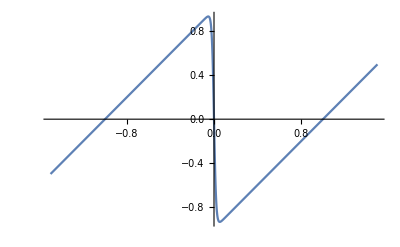

```mathematica
Clear[a,b,c,d,m,k]
k=12;
{a,b,c,d,m}=Sprott[k]["par"];
EqEq=0==Sprott[k]["fun"]/.{yp->0,ypp->0}
Clear[a,b,c,d,m,k]
Plot[y-Tanh[50 y],{y,-1.5,1.5}]
```